# Random PoS reward function

## Constant reward function

```mathematica
constreward[n_,R_,T_]=R/T
```

R/T

## Geometric reward function

```mathematica
geometricreward[n_, R_, T_] = (1 + R)^(n/T) - (1 + R)^((n-1)/T)
```

-(1+R)^((-1+n)/T)+(1+R)^(n/T)

## Random reward function

```mathematica
randomreward[n_, R_, T_] = Random[]*2*R/T
```

0.157828 R

```mathematica
randomdistribution[n_, R_, T_] = BetaDistribution[2,5]*2*R/T
```

2/5 R BetaDistribution[2,5]

## Interest rate function

```mathematica
interestreward[n_, r_, T_] = (1+r/n)^(n*T)
```

(1+r/n)^(n T)

## Comparison

```mathematica
T = 5
n = 20
rewards = List[50*n,25*n,12.5*n,6.25*n,3.125*n]
r =0.03
dataconst= Flatten[Table[Table[constreward[runs, rewards[[i]], n],{runs,0,n}],{i,1,T}]]
datageometric = Flatten[Table[Table[geometricreward[runs, rewards[[i]], n],{runs,0,n}],{i,1,T}]]
datarandom = Flatten[Table[Table[randomreward[runs, rewards[[i]], n],{runs,0,n}],{i,1,T}]]
datarandomdist = Flatten[Table[Table[randomdistribution[runs, rewards[[i]], n],{runs,0,n}],{i,1,T}]]
```

5

20

{1000,500,250.,125.,62.5}

0.03

{50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125}

{1-1/1001^(1/20),-1+1001^(1/20),-1001^(1/20)+1001^(1/10),-1001^(1/10)+1001^(3/20),-1001^(3/20)+1001^(1/5),-1001^(1/5)+1001^(1/4),-1001^(1/4)+1001^(3/10),-1001^(3/10)+1001^(7/20),-1001^(7/20)+1001^(2/5),-1001^(2/5)+1001^(9/20),-1001^(9/20)+√1001,-√1001+1001^(11/20),-1001^(11/20)+1001^(3/5),-1001^(3/5)+1001^(13/20),-1001^(13/20)+1001^(7/10),-1001^(7/10)+1001^(3/4),-1001^(3/4)+1001^(4/5),-1001^(4/5)+1001^(17/20),-1001^(17/20)+1001^(9/10),-1001^(9/10)+1001^(19/20),1001-1001^(19/20),1-1/501^(1/20),-1+501^(1/20),-501^(1/20)+501^(1/10),-501^(1/10)+501^(3/20),-501^(3/20)+501^(1/5),-501^(1/5)+501^(1/4),-501^(1/4)+501^(3/10),-501^(3/10)+501^(7/20),-501^(7/20)+501^(2/5),-501^(2/5)+501^(9/20),-501^(9/20)+√501,-√501+501^(11/20),-501^(11/20)+501^(3/5),-501^(3/5)+501^(13/20),-501^(13/20)+501^(7/10),-501^(7/10)+501^(3/4),-501^(3/4)+501^(4/5),-501^(4/5)+501^(17/20),-501^(17/20)+501^(9/10),-501^(9/10)+501^(19/20),501-501^(19/20),0.241394,0.318207,0.419463,0.552939,0.728888,0.960826,1.26657,1.6696,2.20088,2.90121,3.8244,5.04135,6.64554,8.7602,11.5478,15.2223,20.0662,26.4514,34.8685,45.9638,60.5899,0.214798,0.273557,0.348391,0.443696,0.565072,0.719652,0.916518,1.16724,1.48655,1.8932,2.4111,3.07067,3.91068,4.98048,6.34292,8.07807,10.2879,13.1022,16.6864,21.2511,27.0645,0.187429,0.230662,0.283867,0.349344,0.429924,0.529091,0.651132,0.801323,0.986158,1.21363,1.49356,1.83807,2.26204,2.78381,3.42593,4.21616,5.18867,6.38549,7.85838,9.67101,11.9017}

{157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423}

{400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5]}

```mathematica
plotdata= List[dataconst,datageometric, datarandom, datarandomdist]
```

{{50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,12.5,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125,3.125},{1-1/1001^(1/20),-1+1001^(1/20),-1001^(1/20)+1001^(1/10),-1001^(1/10)+1001^(3/20),-1001^(3/20)+1001^(1/5),-1001^(1/5)+1001^(1/4),-1001^(1/4)+1001^(3/10),-1001^(3/10)+1001^(7/20),-1001^(7/20)+1001^(2/5),-1001^(2/5)+1001^(9/20),-1001^(9/20)+√1001,-√1001+1001^(11/20),-1001^(11/20)+1001^(3/5),-1001^(3/5)+1001^(13/20),-1001^(13/20)+1001^(7/10),-1001^(7/10)+1001^(3/4),-1001^(3/4)+1001^(4/5),-1001^(4/5)+1001^(17/20),-1001^(17/20)+1001^(9/10),-1001^(9/10)+1001^(19/20),1001-1001^(19/20),1-1/501^(1/20),-1+501^(1/20),-501^(1/20)+501^(1/10),-501^(1/10)+501^(3/20),-501^(3/20)+501^(1/5),-501^(1/5)+501^(1/4),-501^(1/4)+501^(3/10),-501^(3/10)+501^(7/20),-501^(7/20)+501^(2/5),-501^(2/5)+501^(9/20),-501^(9/20)+√501,-√501+501^(11/20),-501^(11/20)+501^(3/5),-501^(3/5)+501^(13/20),-501^(13/20)+501^(7/10),-501^(7/10)+501^(3/4),-501^(3/4)+501^(4/5),-501^(4/5)+501^(17/20),-501^(17/20)+501^(9/10),-501^(9/10)+501^(19/20),501-501^(19/20),0.241394,0.318207,0.419463,0.552939,0.728888,0.960826,1.26657,1.6696,2.20088,2.90121,3.8244,5.04135,6.64554,8.7602,11.5478,15.2223,20.0662,26.4514,34.8685,45.9638,60.5899,0.214798,0.273557,0.348391,0.443696,0.565072,0.719652,0.916518,1.16724,1.48655,1.8932,2.4111,3.07067,3.91068,4.98048,6.34292,8.07807,10.2879,13.1022,16.6864,21.2511,27.0645,0.187429,0.230662,0.283867,0.349344,0.429924,0.529091,0.651132,0.801323,0.986158,1.21363,1.49356,1.83807,2.26204,2.78381,3.42593,4.21616,5.18867,6.38549,7.85838,9.67101,11.9017},{157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,157.828,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,78.9138,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,39.4569,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,19.7285,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423,9.86423},{400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],400 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],200 BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],100. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],50. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5],25. BetaDistribution[2,5]}}

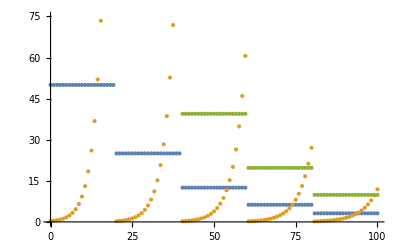

```mathematica
ListPlot[plotdata,PlotRange -> {0, 75}, DataRange->{0,T*n}]
```